### Code to generate the training set and test set

```mathematica
ClearAll["Global`*"];

(* generating random 2D points for the plots *)
getRandomPointsList[range_Integer,n_Integer,i_Integer] := Table[ RandomReal[ range, {n,2}], i ]


(* generating corresponding scattered plots as images *)
getRasterizedPlots[data_] := Map[Rasterize[ListPlot[#], ImageSize->{360,240}] &, data]


(* extracting raw axes from scattered plots *)
getRawAxes[data_] := Map[AlphaChannel[Rasterize[ListPlot[#,PlotStyle->Transparent,LabelStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None,ImageSize->{360,240}]]&, data ]

(* extracting raw laberls from scattered plots*)
getRawLabels[data_,axes_] := MapThread[ImageDifference[Binarize[AlphaChannel[Rasterize[ListPlot[#1, PlotStyle->Transparent, BaseStyle->{Antialiasing->False}], Background->None, ImageSize->{360,240}]],0],#2]&,
{data,axes}
]

(* generating binarized points from scattered plots *)
getBinarizedPoints[data_]:= Map[AlphaChannel[Rasterize[ListPlot[#, AxesStyle->Transparent, BaseStyle->{Antialiasing->False}], Background->None, ImageSize->{360,240}]]&, data]


(* filtering out points that are overlapping with the axes and axes labels *)
getAxes[axes_, binarizedPoints_]:= MapThread[ImageSubtract[#1, #2]&,{axes, binarizedPoints}]

getLabels[binarizedPoints_, labels_]:= MapThread[ImageSubtract[#1, #2]&,{labels, binarizedPoints}]

(* generating backgrounds from scattered plots *)
getBackgrounds[axes_,labels_,binarizedPoints_]:= MapThread[ColorNegate[ImageAdd[#1,#2,#3]]&,{axes,labels,binarizedPoints}]


(* generating image segmentations from scattered plots *)
segmentateImage[background_,axes_,labels_,binarizedPoints_]:= Round[ImageData[ImageAdd@@MapThread[ImageMultiply,{Image[{background, axes, labels, binarizedPoints},"Real32"],{1,2,3,4}}]]]

getSegmentations[dataPoints_]:=Module[{data=dataPoints, binarizedPoints, axes, labels, backgrounds},
binarizedPoints=getBinarizedPoints[data];
axes=getAxes[getRawAxes[data], binarizedPoints];
labels=getLabels[binarizedPoints, getRawLabels[data, axes]];
backgrounds=getBackgrounds[axes, labels, binarizedPoints];
MapThread[segmentateImage[#1, #2, #3, #4]&,{backgrounds, axes, labels, binarizedPoints}]
]

(* generating training data where scattered plots are used as inputs and image segmentations are used as outputs *)
createTrainingData[range_Integer,n_Integer,i_Integer] := Module[{data=getRandomPointsList[range, n, i], plotsImages, segmentations},
plotsImages= getRasterizedPlots[data];
segmentations = getSegmentations[data];
MapThread[Rule[#1, #2]&,{plotsImages, segmentations}]
]
```

```mathematica
getRandomPointsList[10,10,10]
```

{{{4.91772,8.16789},{5.26001,6.69043},{1.00813,2.30941},{1.69454,6.75682},{8.07665,8.1975},{8.16549,0.58776},{0.668847,2.6456},{1.77075,9.61789},{0.76613,0.526055},{7.26925,7.96094}},{{6.26891,9.88259},{3.50914,9.9034},{7.27845,8.17239},{7.42442,6.90777},{1.86877,2.20457},{1.30628,3.0706},{9.83163,8.13342},{0.11022,8.72563},{8.94332,7.23312},{8.69617,2.43789}},{{9.72071,3.88172},{8.92256,3.95358},{0.162639,1.58838},{4.76676,9.25127},{2.15573,7.61001},{0.0662627,7.97559},{3.03884,8.80599},{1.97664,9.1357},{5.46375,5.73032},{3.89664,5.85635}},{{1.70438,7.45844},{0.252208,9.66799},{1.71692,3.28913},{9.72876,4.03279},{4.69812,9.55602},{6.87624,0.552756},{2.9598,5.57552},{4.65094,1.91545},{8.92829,0.449805},{2.42004,6.31289}},{{8.93672,4.51429},{8.8387,8.16287},{3.22078,4.18428},{7.87207,4.76004},{6.48397,7.09299},{5.79772,1.92667},{9.05012,3.40603},{7.41619,3.63499},{4.1609,8.01368},{0.447534,9.80483}},{{0.773238,8.77719},{3.28476,6.81552},{3.33473,1.18577},{1.63759,6.40438},{6.20213,7.30828},{7.42657,1.5241},{0.308813,6.28003},{4.19798,6.26947},{0.815478,8.53834},{0.225378,4.41469}},{{7.02151,7.18784},{6.68877,2.4711},{3.797,8.0959},{3.22413,7.861},{2.75766,0.178635},{8.96646,8.57843},{3.04291,8.78366},{6.64686,4.24513},{3.71503,9.42328},{4.53992,0.648216}},{{7.41573,9.90622},{3.7028,2.18005},{1.52302,6.04336},{9.98088,3.29721},{1.28676,1.6519},{3.33125,2.20142},{6.24884,9.18102},{1.97098,7.15554},{3.14904,4.94017},{7.56186,7.01787}},{{1.77221,6.77893},{7.52411,0.169266},{2.8592,0.916177},{3.44811,9.42467},{6.01826,6.04544},{1.62197,9.95164},{5.83408,8.50311},{4.16581,0.211962},{6.1505,4.755},{0.249136,1.8632}},{{0.771996,9.10914},{1.07625,2.8488},{2.01114,3.81636},{6.47455,2.48551},{3.92701,5.99987},{1.70001,8.48583},{8.16604,6.73349},{2.10582,5.90722},{9.43447,8.85332},{8.33879,2.20308}}}

```mathematica
pts=getRandomPointsList[10,10,10];
```

```mathematica
pts[[1]]
```

{{1.92806,2.84904},{6.29739,1.37156},{4.54364,0.432522},{1.14107,7.72979},{1.7895,5.12321},{6.44197,0.869927},{2.04936,3.80698},{5.97824,5.29843},{2.75374,4.95625},{1.10054,3.89289}}

```mathematica
RandomInteger[{1,10},2]
```

```mathematica
rescale
```

{7,2}

```mathematica
{4,2}*{5,6}
```

{20,12}

```mathematica
Table[x*2,{x,{2,4,6,8}}]
```

{4,8,12,16}

```mathematica
RandomReal[{.1,20},2]
```

{3.45427,10.1316}

```mathematica
getRasterizedPlots[Table[Module[{rescale=RandomReal[{.1,20},2]},
rescale*#&/@pointset],{pointset,getRandomPointsList[10,20,10]}]]
```

Thread::tdlen: Objects of unequal length in {3.24092,0.763497} {{8.81027,1.87152},{9.70817,8.46547},{4.94833,6.65359},{5.11341,2.67289}} cannot be combined.

Thread::tdlen: Objects of unequal length in {3.24092,0.763497} {{2.68346,1.42945},{7.29619,1.59595},{4.50403,4.24852},{5.3159,1.49616}} cannot be combined.

Thread::tdlen: Objects of unequal length in {3.24092,0.763497} {{1.98059,5.16721},{4.4134,7.45116},{0.797308,6.59343},{2.92714,3.20912}} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
getRasterizedPlots[getRandomPointsList[10,10,10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
data=createTrainingData[50,50,1000];//AbsoluteTiming
```

{219.478,Null}

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\wolfram\Desktop\Wangping

```mathematica
Export["data.wl",data]
```

data.wl

```mathematica
trainingSet=Take[data,900];
testSet=Take[data,-100];
```

```mathematica
net=NetModel["Dilated ResNet-22 Trained on Cityscapes Data"]
```

NetGraph[<>]

```mathematica
ourNet=NetReplacePart[net,{"input_0"->NetEncoder[{"Image",{360,240}}],"Output"->NetDecoder[{"Class",Range[1,19],"InputDepth"->3}]}];
```

```mathematica
trainedNet=NetTrain[ourNet,<|"input_0"->First/@trainingSet,"Output"->Last/@trainingSet|>,LossFunction->CrossEntropyLossLayer["Index"],TargetDevice->"GPU"]
```

NetGraph[<>]

```mathematica
testPlot=createTrainingData[50,50,1][[1,1]]
```

-Graphics-

```mathematica
trainedNet[testPlot]//Colorize
```

-Graphics-

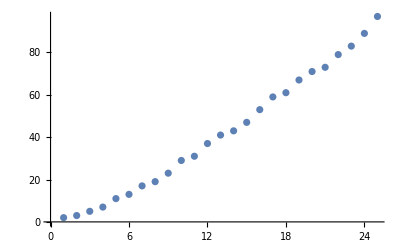
```mathematica
ImageResize[-Graphics-,{360,240}]
```

```mathematica
trainedNet[ImageResize[-Graphics-,{360,240}]]//Colorize
```

-Graphics-

```mathematica
Export["Jofre_Wangping_extract_points_from_plots.wlnet",trainedNet]
```

Jofre_Wangping_extract_points_from_plots.wlnet

```mathematica
Directory[]
```

C:\Users\97587\Documents\GitHub\WSS-Template\Final Project\Drafts\Images

```mathematica
trainedNet=Import["Jofre_Wangping_extract_points_from_plots.wlnet"]
```

NetGraph[<>]

```mathematica
trainedNet[-Graphics-]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},238,{1,358,1}}
 |  |  |  |

```mathematica
labels={"background","axes","labels","data"}
```

{background,axes,labels,data}

```mathematica
Counts@Flatten[%229/.n_Integer:>labels[[n]]]
```

<|background→84746,axes→700,labels→326,data→628|>